```mathematica
alphaRod = 0.4;
alphaSheet = 0.02;
epsilon = 0.1;
```

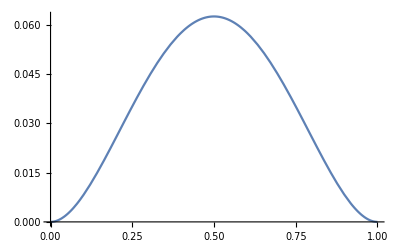

```mathematica
Plot[x^2(x-1)^2,{x,0,1}]
```

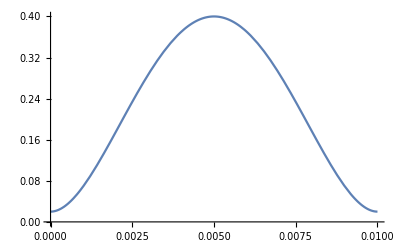

```mathematica
BB = 0.01; 
initFunc[x_]:=x^2(x-BB)^2;
maxVal = initFunc[BB/2];
funcUse[x_]:=(1/maxVal)*(alphaRod-alphaSheet)*initFunc[x]+alphaSheet;
Plot[funcUse[x],{x,0,BB}]
```

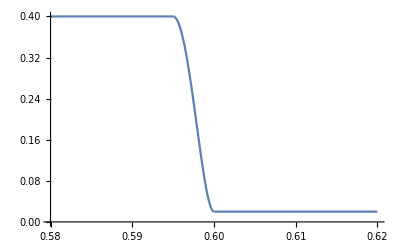

```mathematica
diffConst[x_]:=Piecewise[{{alphaSheet, x < 0.5-epsilon},
{funcUse[x-(0.5-epsilon)],x ≥ 0.5-epsilon && x < 0.5 - epsilon+BB/2},{alphaRod,x ≥ 0.5-epsilon+BB/2 && x < 0.5 + epsilon-BB/2},
{funcUse[x-(0.5+epsilon-BB)],x ≥ 0.5+epsilon-BB/2 && x < 0.5 + epsilon},{alphaSheet,x≥0.5+epsilon}}];
Plot[diffConst[x],{x,0.58,0.62}]
```

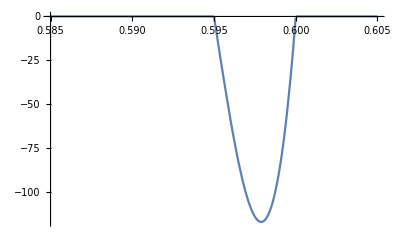

```mathematica
diffConstDeriv[x_]:=D[diffConst[xV],xV]/.{xV->x};
Plot[diffConstDeriv[x],{x,0.585,0.605}]
```

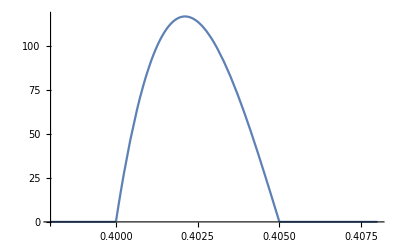

```mathematica
Plot[diffConstDeriv[x],{x,0.398,0.408}]
```

```mathematica
(*This is my unit square system that features a rod in the middle of it*)
```

```mathematica
alphaRod = 0.4;
alphaSheet = 0.02;
epsilon = 0.1;
initF[x_,y_]:= 20*x^2*(x-1)^2*y^2*(y-1)^2; 
systemWithRod = NDSolveValue[{D[u[x,y,t],t]-diffConst[x]*Laplacian[u[x,y,t],{x,y}]-diffConstDeriv[x]*D[u[x,y,t],x]==0,DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0,1},{y,0,1},{t,0,10}];
systemNoRod = NDSolveValue[{D[u[x,y,t],t]-alphaSheet*Laplacian[u[x,y,t],{x,y}]==0,DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0,1},{y,0,1},{t,0,10}];
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
(*3D plot of system*)
Manipulate[Plot3D[{systemNoRod[x,y,t],systemWithRod[x,y,t],0,0.08},{x,0,1},{y,0,1},PlotLegends->{"System without Rod","System with Rod","Zero","Const"}],{t,0,10}]
```

```mathematica
(*2D plot of y=0.5 cross-section*)
Manipulate[Plot[{systemNoRod[x,0.5,t],systemWithRod[x,0.5,t],0,0.08},{x,0,1},PlotLegends->{"System without Rod","System with Rod","Zero","Const"}],{t,0,4}]
```

```mathematica
(*This verifies conservation of energy for both systems*)
Energy[t_]:=NIntegrate[systemWithRod[x,y,t],{x,0,1},{y,0,1}];
Table[Energy[t],{t,0,5,1}]
Energy2[t_]:=NIntegrate[systemNoRod[x,y,t],{x,0,1},{y,0,1}];
Table[Energy2[t],{t,0,5,1}]
```

{0.0222233,0.0222233,0.0222233,0.0222233,0.0222233,0.0222233}

{0.0222233,0.0222233,0.0222233,0.0222233,0.0222233,0.0222233}

```mathematica
(*Derivatives in X and Y direction so we can obtain the fluxes*)
```

```mathematica
XderivNonUniformDiffusion[x_,y_,t_]:=D[systemWithRod[xV,yV,tV],xV]/.{tV->t,xV->x,yV->y};
YderivNonUniformDiffusion[x_,y_,t_]:=D[systemWithRod[xV,yV,tV],yV]/.{tV->t,xV->x,yV->y};
XderivUniformDiffusion[x_,y_,t_]:=D[systemNoRod[xV,yV,tV],xV]/.{tV->t,xV->x,yV->y};
YderivUniformDiffusion[x_,y_,t_]:=D[systemNoRod[xV,yV,tV],yV]/.{tV->t,xV->x,yV->y};
```

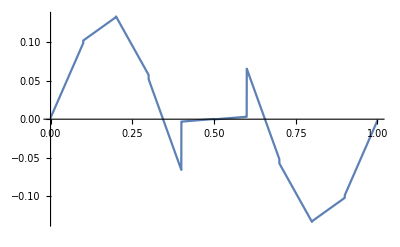

```mathematica
(*Horizontal Diffusion in middle of system*)
tVV=0.4;
Plot[XderivNonUniformDiffusion[x,0.5,tVV],{x,0,1}]
```

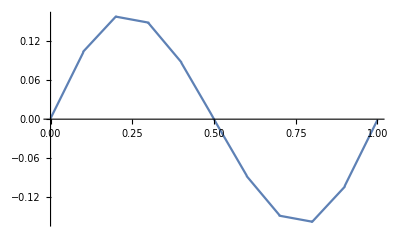

```mathematica
(*Horizontal Diffusion in middle of system for uniform case*)
Plot[XderivUniformDiffusion[x,0.5,tVV],{x,0,1}]
```

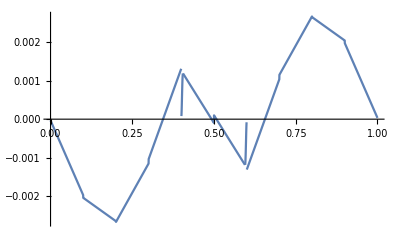

```mathematica
(*Horizontal Flux in middle of system*)
Plot[-XderivNonUniformDiffusion[x,0.5,tVV]*diffConst[x],{x,0,1}]
```

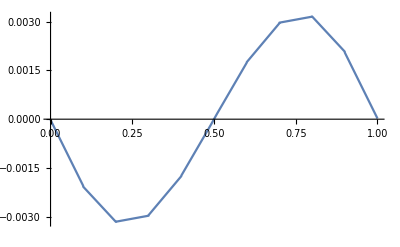

```mathematica
(*Horizontal Flux in middle of system for uniform case*)
Plot[-XderivUniformDiffusion[x,0.5,tVV]*alphaSheet,{x,0,1}]
```

```mathematica
(*Diffusion at borders. should be near zero*)
Table[YderivNonUniformDiffusion[x,1,tVV],{x,0,1,.1}]
Table[YderivNonUniformDiffusion[x,0,tVV],{x,0,1,.1}]
Table[XderivNonUniformDiffusion[0,y,tVV],{y,0,1,.1}]
Table[XderivNonUniformDiffusion[1,y,tVV],{y,0,1,.1}]
```

{-0.00107796,-0.00085832,-0.0000529501,0.00107793,-0.000138623,-0.000232363,-0.000138623,0.00107793,-0.0000529501,-0.00085832,-0.00107796}

{0.00107796,0.00085832,0.0000529501,-0.00107793,0.000138623,0.000232363,0.000138623,-0.00107793,0.0000529501,0.00085832,0.00107796}

{0.000426179,0.000523093,0.000806094,0.00119876,0.0015367,0.0016684,0.0015367,0.00119876,0.000806094,0.000523093,0.000426179}

{-0.000426179,-0.000523093,-0.000806094,-0.00119876,-0.0015367,-0.0016684,-0.0015367,-0.00119876,-0.000806094,-0.000523093,-0.000426179}

```mathematica
(*Diffusion at borders for uniform case as comparison. should be near zero*)
Table[YderivUniformDiffusion[x,1,tVV],{x,0,1,.1}]
Table[YderivUniformDiffusion[x,0,tVV],{x,0,1,.1}]
Table[XderivUniformDiffusion[0,y,tVV],{y,0,1,.1}]
Table[XderivUniformDiffusion[1,y,tVV],{y,0,1,.1}]
```

{-0.0011164,-0.00107476,-0.00101796,-0.00103093,-0.00108928,-0.00111984,-0.00108928,-0.00103093,-0.00101796,-0.00107476,-0.0011164}

{0.0011164,0.00107476,0.00101796,0.00103093,0.00108928,0.00111984,0.00108928,0.00103093,0.00101796,0.00107476,0.0011164}

{0.0011164,0.00107476,0.00101796,0.00103093,0.00108928,0.00111984,0.00108928,0.00103093,0.00101796,0.00107476,0.0011164}

{-0.0011164,-0.00107476,-0.00101796,-0.00103093,-0.00108928,-0.00111984,-0.00108928,-0.00103093,-0.00101796,-0.00107476,-0.0011164}